## Thomas and Cover, 7.1.2

```mathematica
S1 = -p  q1  Log[p q1]-p(1-q1)  Log[p(1-q1)]-(1-p)q2  Log[(1-p)q2] - (1-p)(1-q2)Log[(1-p)(1-q2)];
S2 = -p(q1 Log[q1]+(1-q1)Log[1-q1])-(1-p)(q2 Log[q2] + (1-q2)Log[1-q2]);
MI = FullSimplify[S1-S2]
```

p (-(-1+q1) Log[1-q1]+q1 Log[q1])-p q1 Log[p q1]+p (-1+q1) Log[p-p q1]-(-1+p) (-1+q2) Log[(-1+p) (-1+q2)]+(1-p) (-(-1+q2) Log[1-q2]+q2 Log[q2])+(-1+p) q2 Log[q2-p q2]

```mathematica
Maximize[{MI/Log[2] /. {q1-> 1/2, q2-> 1/3}, 0 ≤ p≤ 1}, p]//N
```

{1.,{p→0.5}}

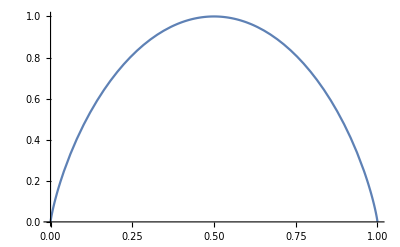

```mathematica
Plot[MI/Log[2] /. {q1-> 1/2, q2-> 1/3}, {p,0,1}, PlotRange-> All]
```